```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 18:47:41
using xCellerator 0.90 and XSSA 1204002

## CellNeighbors-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

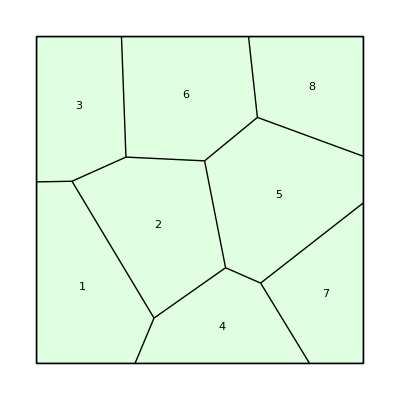

```mathematica
w=TemplateRandomSquareGrid[5,{0,0},{100,100}];
ShowTissue[w, "CellNumbers"->True]
```

```mathematica
CellNeighbors[w, 5]
```

{2,4,6,7,8}

```mathematica
CellNeighbors[w, 4]
```

{1,2,5,7}

```mathematica
CellNeighbors[w]
```

{{2,3,4},{1,3,4,5,6},{1,2,6},{1,2,5,7},{2,4,6,7,8},{2,3,5,8},{4,5},{5,6}}